# Pseudoinverse

## 3D Example

```mathematica
f[x1_,x2_]:=3+0.5*x1+10*x1*x2+2*x2^2
```

```mathematica
Plot3D[f[x1,x2],{x1,-5,5},{x2,-5,5}]
```

-Graphics3D-

```mathematica
samples=Flatten[Table[{x1,x2,f[x1,x2]},{x1,-5,5,0.5},{x2,-5,5,0.5}],1];
```

```mathematica
SeedRandom[1337];
samplesNoise=(#+RandomReal[{-2,2}])&/@samples;
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"data3D.mat"}],{"data"->samplesNoise},"LabeledData"];*)
```

## 2D Example

The data in the file data2D.mat is generated according to the following function:

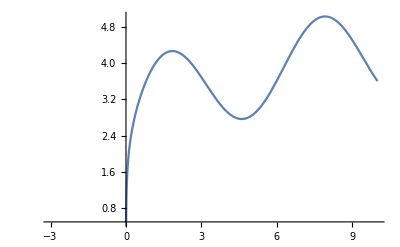

```mathematica
Plot[3+Sin[x]+0.5*Log[x],{x,-3,10}]
```